```mathematica
binomial[z_,k_]:=binomial[z,k]=Product[z-j,{j,0,k-1}]/k!
Dnka[n_,0,a_]:=UnitStep[n-1]
Dnka[n_,1,a_]:=Dnka[n,1,a]=Floor[n]-a
Dnka[n_,2,a_]:=Dnka[n,2,a]=Sum[1+2 (Dnka[Floor[n/m],1,m]),{m,a+1,Floor[n^(1/2)]}]
Dnka[n_,k_,a_]:=Dnka[n,k,a]=Sum[1+k Dnka[Floor[n/(m^(k-1))],1,m]+Sum[binomial[k,j] Dnka[Floor[n/(m^j)],k-j,m],{j,1,k-2}],{m,a+1,Floor[n^(1/k)]}]

Dnz[n_,z_]:=Expand@Sum[binomial[z,k]Dnka[n,k,1],{k,0,Log2@n}]
dz[n_,z_]:=dz[n,z]=Product[(-1)^p[[2]] bin[-z,p[[2]]],{p,FI[n]}]
dnz[n_,z_]:=Dnz[n,z]-Dnz[n-1,z]
DnzRoots[n_]:=If[(c=Exponent[f=Dnz[n,z],z])==0,{},If[c==1,List@NRoots[f==0,z][[2]],List@@NRoots[f==0,z][[All,2]]]]
dnzRoots[n_]:=If[(c=Exponent[f=dz[n,z],z])==0,{},If[c==1,List@NRoots[f==0,z][[2]],List@@NRoots[f==0,z][[All,2]]]]
DnzR[n_,z_]:=Chop@Expand@Product[1-z/rho,{rho,DnzRoots[n]}]
```

```mathematica
DnzRoots[100000000]
```

{-7494.07,-1440.44,-281.526,-37.2362-148.713 ⅈ,-37.2362+148.713 ⅈ,-35.5639,-13.9034-54.5839 ⅈ,-13.9034+54.5839 ⅈ,-13.5241-33.6412 ⅈ,-13.5241+33.6412 ⅈ,-11.5772-12.0093 ⅈ,-11.5772+12.0093 ⅈ,-6.16326-16.2264 ⅈ,-6.16326+16.2264 ⅈ,-4.59605-8.12566 ⅈ,-4.59605+8.12566 ⅈ,-4.13439-4.72012 ⅈ,-4.13439+4.72012 ⅈ,-3.44066-2.91838 ⅈ,-3.44066+2.91838 ⅈ,-2.68701-1.52872 ⅈ,-2.68701+1.52872 ⅈ,-1.94007-0.419915 ⅈ,-1.94007+0.419915 ⅈ,-0.99477,-1.73548×10^-7}

```mathematica
a2 := {-7494.069914345595,-1440.4409044583288,-281.5257697989761,-37.23624188545817-148.7128809232404 ⅈ,-37.23624188545817+148.7128809232404 ⅈ,-35.563903002932584,-13.903356146346544-54.58386377231285 ⅈ,-13.903356146346544+54.58386377231285 ⅈ,-13.524093734436974-33.6412254304076 ⅈ,-13.524093734436974+33.6412254304076 ⅈ,-11.577243234325424-12.009344141541174 ⅈ,-11.577243234325424+12.009344141541174 ⅈ,-6.1632575936044525-16.22644747537662 ⅈ,-6.1632575936044525+16.22644747537662 ⅈ,-4.596047565793488-8.125664873762274 ⅈ,-4.596047565793488+8.125664873762274 ⅈ,-4.13439045189022-4.720122122665344 ⅈ,-4.13439045189022+4.720122122665344 ⅈ,-3.4406566978797453-2.918382537307335 ⅈ,-3.4406566978797453+2.918382537307335 ⅈ,-2.6870149652152633-1.5287204893576303 ⅈ,-2.6870149652152633+1.5287204893576303 ⅈ,-1.9400667098251676-0.419915062049149 ⅈ,-1.9400667098251676+0.419915062049149 ⅈ,-0.9947702510510221}
```

```mathematica
Product[ 1-1/p,{p,a2}]
```

17.3548+3.33067×10^-16 ⅈ

```mathematica
DnzRoots[1000]
```

{-145.722,-8.80186-14.3448 ⅈ,-8.80186+14.3448 ⅈ,-4.45483-3.16845 ⅈ,-4.45483+3.16845 ⅈ,-2.04875-1.06859 ⅈ,-2.04875+1.06859 ⅈ,-0.961602,-0.00572997}

```mathematica
Table[Chop@Product[If[Abs[p]<.3,1, 1-1/p],{p,DnzRoots[10^k]}],{k,1,8}]//TableForm
```

1.79323
3.58701
5.69732
8.02866
10.3821
12.7234
15.0416
17.3548

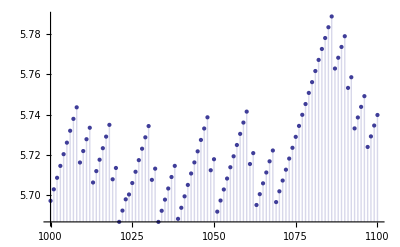

```mathematica
DiscretePlot[Chop@Product[If[Abs[p]<.3,1, 1-1/p],{p,DnzRoots[k]}],{k,1000,1100}]
```

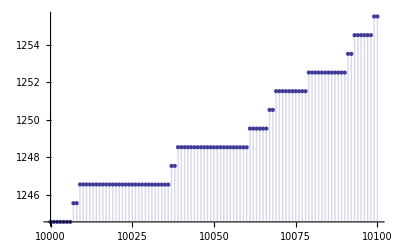

```mathematica
DiscretePlot[Product[If[Abs[p]>.3,1, -1/p],{p,DnzRoots[k]}],{k,10000,10100}]
```

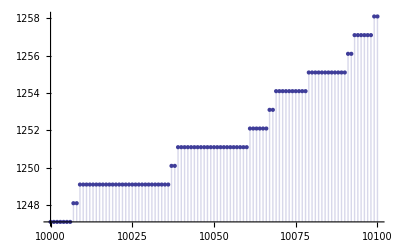

```mathematica
DiscretePlot[Sum[-1/p,{p,DnzRoots[k]}],{k,10000,10100}]
```

```mathematica
binomial[z_,k_]:=binomial[z,k]=Product[z-j,{j,0,k-1}]/k!
Ds[n_,0,s_,a_]:=UnitStep[n-1]
Ds[n_,1,s_,a_]:=Ds[n,1,s,a]=HarmonicNumber[Floor[n],s]-HarmonicNumber[a,s]
Ds[n_,2,s_,a_]:=Ds[n,2,s,a]=Sum[(m^(-2s))+2(m^-s) (Ds[Floor[n/m],1,s,m]),{m,a+1,Floor[n^(1/2)]}]
Ds[n_,k_,s_,a_]:=Ds[n,k,s,a]=Sum[(m^(-s k))+k(m^(-s(k-1))) Ds[Floor[n/(m^(k-1))],1,s,m]+Sum[binomial[k,j] (m^-s)^j Ds[Floor[n/(m^j)],k-j,s,m],{j,1,k-2}],{m,a+1,Floor[n^(1/k)]}]
Dnsz[n_,s_,z_]:=Expand@Sum[binomial[z,k]Ds[n,k,s,1],{k,0,Log2@n}]
Dnsza[n_,s_,z_]:=Expand@Sum[j^-s dz[j,z],{j,1,n}]

Dns112z[n_,s_,z_]:=Expand@Sum[(-1)^j binomial[z,j] 2^(j(1-s))Dnsz[n/(2^j),s,z],{j,0,Log2@n}]
Dns112za[n_,s_,z_]:=Expand@Sum[(-1)^j binomial[z,j] 2^(j(1-s))Dnsza[n/(2^j),s,z],{j,0,Log2@n}]

Dns112zZeros[n_,s_]:=If[(c=Exponent[f=Dns112z[n,s,z],z])==0,{},If[c==1,List@NRoots[f==0,z][[2]],List@@NRoots[f==0,z][[All,2]]]]
Dns112zR[n_,s_,z_]:=Chop@Expand@Product[1-z/rho,{rho,Dns112zZeros[n,s]}]
```

```mathematica
Dns112zZeros[100000000,N@ZetaZero[1]]
```

{-23.4433+115.492 ⅈ,-3.00749+7.24046 ⅈ,-0.00399172-0.0024432 ⅈ,1.+3.6082×10^-6 ⅈ,1.59804+38.0367 ⅈ,1.61973-1.50287 ⅈ,2.00164-0.0052567 ⅈ,2.70904+0.134875 ⅈ,3.0931-8.44949 ⅈ,3.1986-1.21641 ⅈ,3.56358+1.39473 ⅈ,4.17529-3.86039 ⅈ,4.4097+16.3853 ⅈ,4.60627+3.92814 ⅈ,5.18591+0.00864523 ⅈ,9.63811-0.0407831 ⅈ,12.2774-154.546 ⅈ,12.4618-21.1794 ⅈ,21.8501+3.95519 ⅈ,24.4498-2.96747 ⅈ,32.8255-0.284314 ⅈ,66.7753-26.1226 ⅈ,68.0094+67.8245 ⅈ,87.9623-5862.85 ⅈ,133.035-68.5173 ⅈ,820.076-843.833 ⅈ}

```mathematica
dnzRoots[100000000]
```

{-7.,-7.,-6.,-6.,-5.,-5.,-4.,-4.,-3.,-3.,-2.,-2.,-1.,-1.,0.,0.}

```mathematica
dz[1000000,z]
```

((-5-z)^2 (-4-z)^2 (-3-z)^2 (-2-z)^2 (-1-z)^2 z^2)/518400

```mathematica
dzz[n_,s_,z_]:=n^-s Product[(-1)^p[[2]] bin[-z,p[[2]]],{p,FI[n]}]
dzzRoots[n_,s_]:=If[(c=Exponent[f=dzz[n,s,z],z])==0,{},If[c==1,List@NRoots[f==0,z][[2]],List@@NRoots[f==0,z][[All,2]]]]
```

```mathematica
dzz[100,0,z]
```

1/4 (-1-z)^2 z^2

```mathematica
Dns112zR[100,1,z]-Dns112zR[99,1,z]
```

0.-2.77556×10^-16 z-0.0075 z^2-0.005 z^3+0.0025 z^4

```mathematica
FullSimplify@(Dns112z[100,ZetaZero[1],z]-Dns112z[99,ZetaZero[1],z])
```

4^(-1-ZetaZero[1]) 25^(-ZetaZero[1]) (-3+z) z^2 (1+z)

```mathematica
Dns112zZeros[100,1]
```

{-2.77849,1.65264-2.69167 ⅈ,1.65264+2.69167 ⅈ,4.3873,9.82074-5.46414 ⅈ,9.82074+5.46414 ⅈ}

```mathematica
Animate[Graphics[Table[{ColorData["RustTones"][n/100],Point[{Re[#],Im[#]}]}&/@Dns112zZeros[n,.3+j I],{n,10000,10000}],Frame->True,PlotRange->{{0-4,2+4},{-1-4,1+4}}],{j,14,32,.01}]
```

```mathematica
N@ZetaZero[1]
```

0.5+14.1347 ⅈ

```mathematica
Dns112zZeros[100,1]
```

{-2.77849,1.65264-2.69167 ⅈ,1.65264+2.69167 ⅈ,4.3873,9.82074-5.46414 ⅈ,9.82074+5.46414 ⅈ}

```mathematica
pts=Table[{Point[{Re[#],Im[#]}]}&/@Dns112zZeros[1000,.5+n I],{n,14,32, .03}];
```

```mathematica
pts[[2]]
```

{{Point[{-2.46695,1.07716}]},{Point[{0.529164,-0.230124}]},{Point[{1.12859,0.204044}]},{Point[{1.98993,-0.74285}]},{Point[{2.13135,0.95397}]},{Point[{4.89599,-0.648908}]},{Point[{11.7524,-1.75238}]},{Point[{17.1052,15.4425}]},{Point[{90.9615,-53.0174}]}}

```mathematica
ListAnimate[Table[Graphics[ptsrf[[k]],Frame->True,Axes->True,AxesOrigin->{1,0}, PlotRange->{{0-2,2+2},{-1-2,1+2}}],{k,1,Length[ptsrf]}]]
```

```mathematica
Length[ptsa]
```

1667

```mathematica
pts4=Table[{Point[{Re[#],Im[#]}]}&/@Dns112zZeros[1000,.4+n I],{n,14,32, .03}];
pts6=Table[{Point[{Re[#],Im[#]}]}&/@Dns112zZeros[1000,.6+n I],{n,14,32, .03}];
pts1=Table[{Point[{Re[#],Im[#]}]}&/@Dns112zZeros[1000,1+n I],{n,14,32, .03}];
```

```mathematica
pts2=Table[{Point[{Re[#],Im[#]}]}&/@Dns112zZeros[1000,.2+n I],{n,14,32, .03}];
```

```mathematica
ptsa=Table[{Point[{Re[#],Im[#]}]}&/@Dns112zZeros[1000,.5+n I],{n,0,50, .03}];
```

```mathematica
ptsr=Table[{Point[{Re[#],Im[#]}]}&/@Dns112zZeros[100000,.5+n I],{n,13,32,.05 }];
```

```mathematica
ptst=Table[{Point[{Re[#],Im[#]}]}&/@Dns112zZeros[100000,n+14.134725141734695 ⅈ],{n,0,5,.03}];
```

```mathematica
N@ZetaZero[29]
```

0.5+98.8312 ⅈ

```mathematica
ptsg=Table[{Point[{Re[#],Im[#]}]}&/@Dns112zZeros[100000,n+20 ⅈ],{n,0,3,.03}];
```

```mathematica
ptsr[[1]]
```

{{Point[{-0.755668,2.76242}]},{Point[{0.0914007,-0.0752522}]},{Point[{0.450741,0.349267}]},{Point[{1.53138,-0.821849}]},{Point[{2.31499,-7.52807}]},{Point[{2.44116,2.37914}]},{Point[{2.9159,-1.76289}]},{Point[{4.31139,-0.986764}]},{Point[{6.08043,0.263259}]},{Point[{9.83916,12.1791}]},{Point[{14.3549,42.6005}]},{Point[{17.499,-6.14424}]},{Point[{18.2166,2.53785}]},{Point[{47.1514,-22.9204}]},{Point[{123.952,-122.607}]},{Point[{140.822,187.882}]}}

```mathematica
ptsrf=Table[{Point[{Re[#],Im[#]}]}&/@Dns112zZeros[100000,.5+n I],{n,0,100,.05 }];
```

```mathematica
Expand@Sum[ n^(.5+3I)dz[n,z],{n,1,100000}]
```

(1.+0. ⅈ)-(339784.-755827. ⅈ) z-(1.01599×10^6-2.22564×10^6 ⅈ) z^2-(1.27993×10^6-2.70071×10^6 ⅈ) z^3-(888053.-1.8117×10^6 ⅈ) z^4-(392502.-759690. ⅈ) z^5-(114201.-210752. ⅈ) z^6-(23607.5-40139.4 ⅈ) z^7-(3309.46-5303.18 ⅈ) z^8-(343.29-489.395 ⅈ) z^9-(23.2221-31.114 ⅈ) z^10-(1.13919-1.33696 ⅈ) z^11-(0.0343179-0.0377698 ⅈ) z^12-(0.000708362-0.000633775 ⅈ) z^13-(8.96127×10^-6-6.53149×10^-6 ⅈ) z^14-(3.96572×10^-8-2.46872×10^-8 ⅈ) z^15-(2.42609×10^-10-2.85282×10^-11 ⅈ) z^16

```mathematica
Expand@Dns112za[100000,.5+I,z]
```

(1.+0. ⅈ)+(1.13474+2.10739 ⅈ) z-(6.07616+7.95427 ⅈ) z^2+(9.72613+13.1162 ⅈ) z^3-(8.15909+11.2965 ⅈ) z^4+(4.05033+5.67129 ⅈ) z^5-(1.25553+1.75194 ⅈ) z^6+(0.247138+0.336905 ⅈ) z^7-(0.0307918+0.0396298 ⅈ) z^8+(0.00243475+0.0027785 ⅈ) z^9-(0.000125607+0.000113519 ⅈ) z^10+(4.23162×10^-6+2.29327×10^-6 ⅈ) z^11-(1.00326×10^-7+1.78131×10^-8 ⅈ) z^12+(2.21115×10^-9+9.15285×10^-10 ⅈ) z^13-(3.85328×10^-11+3.77593×10^-11 ⅈ) z^14+(3.04746×10^-13+4.03536×10^-13 ⅈ) z^15-(1.15218×10^-15+1.95429×10^-15 ⅈ) z^16

```mathematica
ListAnimate[Table[Graphics[ptsrf[[k]],Frame->True,Axes->True,AxesOrigin->{1,0}, PlotRange->{{-.3,1.3},{-.8,.8}}],{k,1,Length[ptsrf]}]]
```

```mathematica
ptsre=Table[{Point[{Re[#],Im[#]}]}&/@Dns112zZeros[100000,.5+n I],{n,95,105,.005 }];
```

$Aborted